```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
nPoints=1000;
```

```mathematica
rawDataR=Import["rTrace4.txt","Table"];
datasR = Table[rawDataR[[n]],{n,3,Length[rawDataR]}];
points0=Table[datasR[[i,1]],{i,1,nPoints}];
points1=Table[datasR[[i,8]],{i,1,nPoints}];
```

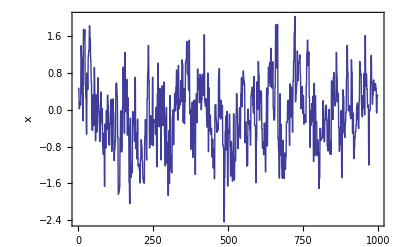

```mathematica
modelR0Plot=ListPlot[points0,Joined->True,DataRange->{0,nPoints},PlotStyle->Thick,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {"",Style["x",Bold]}]
```

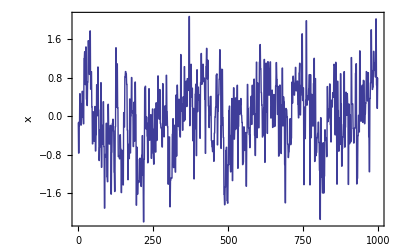

```mathematica
modelR0Plot=ListPlot[points1,Joined->True,DataRange->{0,nPoints},PlotStyle->Thick,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {"",Style["x",Bold]}]
```

```mathematica
rawDataR=Import["rTrace1.txt","Table"];
datasR = Table[rawDataR[[n]],{n,3,Length[rawDataR]}];
points=Table[datasR[[i,1]],{i,1,nPoints}];
```

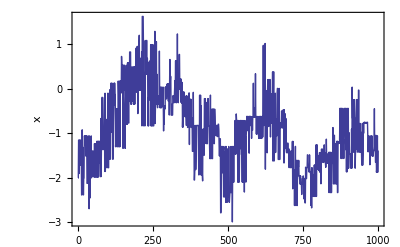

```mathematica
modelR1Plot=ListPlot[points,Joined->True,DataRange->{0,nPoints},PlotStyle->Thick,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {"",Style["x",Bold]}]
```

```mathematica
rawDataR=Import["rTrace10.txt","Table"];
datasR = Table[rawDataR[[n]],{n,3,Length[rawDataR]}];
points=Table[datasR[[i,1]],{i,1,nPoints}];
```

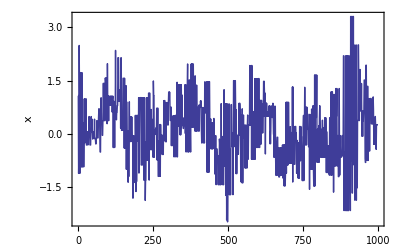

```mathematica
modelR10Plot=ListPlot[points,Joined->True,DataRange->{0,nPoints},PlotStyle->Thick,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {"",Style["x",Bold]}]
```

```mathematica
rawDataR=Import["rTrace100.txt","Table"];
datasR = Table[rawDataR[[n]],{n,3,Length[rawDataR]}];
points=Table[datasR[[i,1]],{i,1,nPoints}];
```

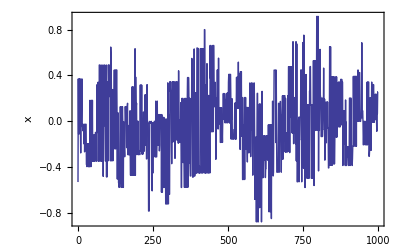

```mathematica
modelR100Plot=ListPlot[points,Joined->True,DataRange->{0,nPoints},PlotStyle->Thick,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {"",Style["x",Bold]}]
```